## Serie de Tylor

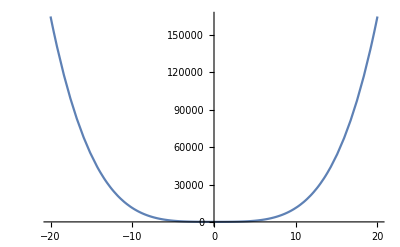

1584804030954+5649898319 (-1122+x)+7553316 (-1122+x)^2+4488 (-1122+x)^3+(-1122+x)^4

-Graphics-

2579172

2579172

```mathematica
f[x_]=x^4+12 x^2-x+12;
a=1;
gradoTy=4;
Aprox=40;
g[x_]=f[a]+∑_(n=1)^gradoTy (((D[f[x],{x,n}]/.x->a)*((x-a)^n))/n!);
Plot[f[x],{x,-20,20}]
g[x]
Plot[g[x],{x,-20,20}]
f[Aprox]
g[Aprox]
```